```mathematica
LLdielectric[Q_,δ_,qf_] = (1 + (2/(3.14159*qf)) * (1/Q^2 + (δ/(2 Q^3))*(ArcTan[(2*Q+Q^2)/δ] + ArcTan[(2*Q-Q^2)/δ]) + (δ^2/(8 Q^5) + 1/(2 Q^3) - 1/(8Q))*(Log[(δ^2 + (2Q + Q^2)^2)]-Log[(δ^2 - (2Q + Q^2)^2)])))
```

1+(0.63662 (1/Q^2+(δ (ArcTan[(2 Q-Q^2)/δ]+ArcTan[(2 Q+Q^2)/δ]))/(2 Q^3)+(1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5)) (-Log[-(2 Q+Q^2)^2+δ^2]+Log[(2 Q+Q^2)^2+δ^2])))/qf

```mathematica
LLdielectric[0.4,0.4,1]
```

11.4432-18.9063 ⅈ

```mathematica
SecondOrder[Q_,δ_]= ((0.5* (2 Q-Q^2)^4)/δ^4-(0.5* (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5)) - 1/Q^2
```

-1/Q^2+((0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))

```mathematica
LLdie2[Q_,δ_] = 4/δ^2-Q^2/δ^2
```

4/δ^2-Q^2/δ^2

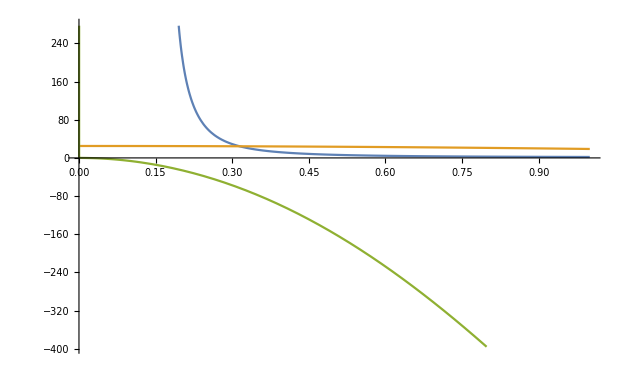

```mathematica
Plot[{Re[LLdielectric[Q,0.4,1]],LLdie2[Q,0.4], SecondOrder[Q,0.4]},{Q,0,1}]
```

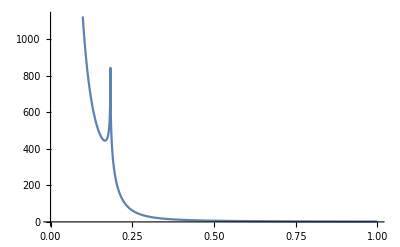

```mathematica
Plot[Re[LLdielectric[Q,0.4,1]],{Q,0,1}]
```

```mathematica
Kdielectric[Q_,A_,B_] = A * (Q^2/(Q^2+ B^2))
```

(A Q^2)/(B^2+Q^2)

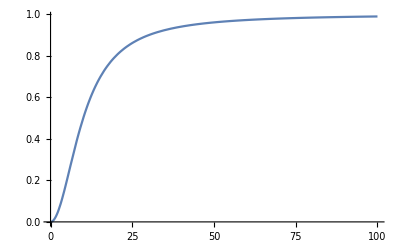

```mathematica
Plot[Kdielectric[Q,1,10],{Q,0,100},PlotRange->All]
```

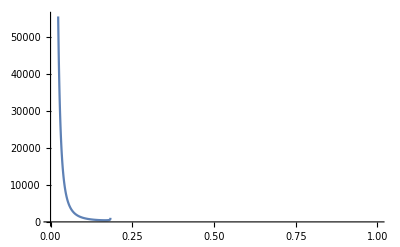

```mathematica
Plot[LLdielectric[Q,0.4],{Q,0,1}]
```

```mathematica
(δ^2/(8*Q^5) + 1/(2*Q^3) - 1/(8*Q))*((2*Q + Q^2)^2/(δ^2) - (2*Q - Q^2)^2/(δ^2))
```

(-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))

```mathematica
Simplify[(-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))]
```

1/Q^2+4/δ^2-Q^2/δ^2

```mathematica
(1/Q^2) - (2/Q^2)+1/Q^2+4/δ^2-Q^2/δ^2
```

4/δ^2-Q^2/δ^2

```mathematica
(* do to one higher order
```

```mathematica
(δ^2/(8*Q^5) + 1/(2*Q^3) - 1/(8*Q))*((2*Q + Q^2)^2/(δ^2) - 0.5*((2*Q + Q^2)^2/(δ^2))^2- (2*Q - Q^2)^2/(δ^2) + 0.5*((2*Q - Q^2)^2/(δ^2))^2)
```

((0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))

```mathematica
Simplify[((0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))]
```

```mathematica
0.+1./Q^2+(1. Q^6)/δ^4-(2. Q^2 (8.+1. δ^2))/δ^4 - 1/Q^2
```

0.+(1. Q^6)/δ^4-(2. Q^2 (8.+1. δ^2))/δ^4

```mathematica
FullSimplify[0.+(1. Q^6)/δ^4-(2. Q^2 (8.+1. δ^2))/δ^4]
```

0.+(Q^2 (-16.+1. Q^4-2. δ^2))/δ^4

```mathematica
(*check for delta = 0 divergence
```

```mathematica
first[Q_,δ_] =-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2
```

-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2

```mathematica
second[Q_,δ_] = (0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2
```

```mathematica
(0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2
third[Q_,δ_] = (0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2 + (1/3)*(((2 Q+Q^2)^2)/δ^2)^3 - (1/3)*(((2 Q-Q^2)^2)/δ^2)^3
```

(0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2

-((2 Q-Q^2)^6)/(3 δ^6)+((2 Q+Q^2)^6)/(3 δ^6)+(0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2

```mathematica
exact[Q_,δ_] = Log[1+((2 Q+Q^2)^2)/δ^2] - Log[1 + ((2 Q-Q^2)^2)/δ^2]
```

-Log[1+((2 Q-Q^2)^2)/δ^2]+Log[1+((2 Q+Q^2)^2)/δ^2]

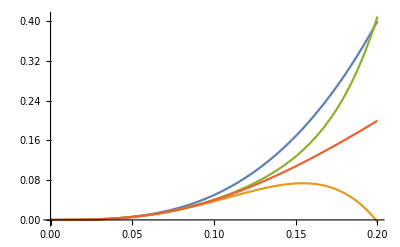

```mathematica
Plot[{first[Q,0.4], second[Q,0.4], third[Q,0.4], exact[Q,0.4]}, {Q,0,0.2}]
```

```mathematica
ThirdOrderLL[Q_,δ_] = 1 + (  (-1/Q^2) +  (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))*((0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2 + (1/3)*(((2 Q+Q^2)^2)/δ^2)^3 - (1/3)*(((2 Q-Q^2)^2)/δ^2)^3) )
```

1-1/Q^2+(-((2 Q-Q^2)^6)/(3 δ^6)+((2 Q+Q^2)^6)/(3 δ^6)+(0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))

```mathematica
Simplify[1-1/Q^2+(-((2 Q-Q^2)^6)/(3 δ^6)+((2 Q+Q^2)^6)/(3 δ^6)+(0.5 (2 Q-Q^2)^4)/δ^4-(0.5 (2 Q+Q^2)^4)/δ^4-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2) (1/(2 Q^3)-1/(8 Q)+δ^2/(8 Q^5))]
```

(-9.33333 Q^8-1. Q^10-2. Q^2 δ^4+δ^6+Q^6 (37.3333+2. δ^2)+Q^4 (64.+13.3333 δ^2))/δ^6

```mathematica
ThirdOrderLLSimp[Q_,δ_]= 1/δ^6(-9.333333333333334 Q^8-1. Q^10-2. Q^2 δ^4+δ^6+Q^6 (37.333333333333336+2. δ^2)+Q^4 (64.+13.333333333333334 δ^2))
```

(-9.33333 Q^8-1. Q^10-2. Q^2 δ^4+δ^6+Q^6 (37.3333+2. δ^2)+Q^4 (64.+13.3333 δ^2))/δ^6

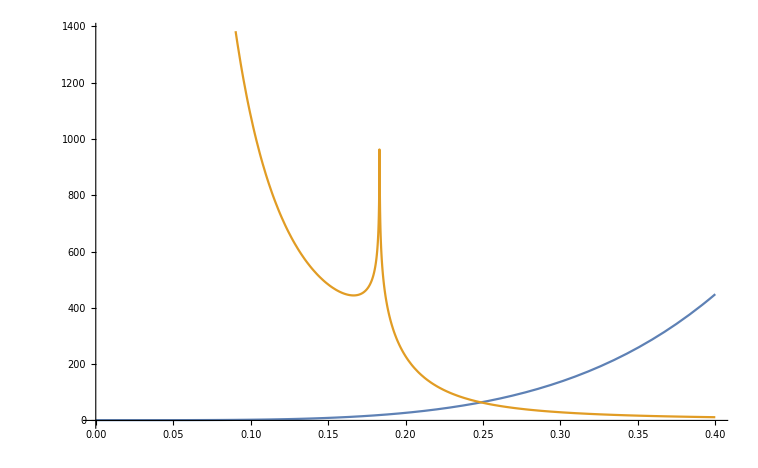

```mathematica
Plot[{Re[ThirdOrderLLSimp[Q,0.4]],Re[LLdielectric[Q,0.4,1]]},{Q,0,0.4}]
```

```mathematica
x=1+((2 Q+Q^2)^2)/δ^2
y=1+((2 Q-Q^2)^2)/δ^2
```

1+((2 Q+Q^2)^2)/δ^2

1+((2 Q-Q^2)^2)/δ^2

```mathematica
Series[Log[1+z], {z,0,10}]
```

```mathematica
Logterm[z_]= z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+z^9/9-z^10/10+O[z]^11
```

z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+z^9/9-z^10/10+O[z]^11

```mathematica
Logterm2[z_]= z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+z^9/9-z^10/10
```

z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+z^9/9-z^10/10

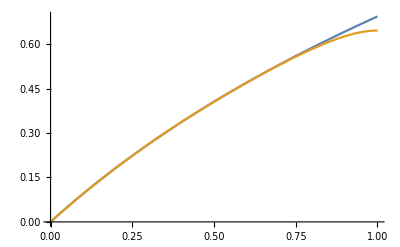

```mathematica
Plot[{Log[1+z],Logterm2[z]},{z,0,1}]
```

```mathematica
Logterm2[x]
```

1-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10+((2 Q+Q^2)^2)/δ^2

```mathematica
Logterm2[x]-Logterm2[y]
```

1/2 (1+((2 Q-Q^2)^2)/δ^2)^2-1/3 (1+((2 Q-Q^2)^2)/δ^2)^3+1/4 (1+((2 Q-Q^2)^2)/δ^2)^4-1/5 (1+((2 Q-Q^2)^2)/δ^2)^5+1/6 (1+((2 Q-Q^2)^2)/δ^2)^6-1/7 (1+((2 Q-Q^2)^2)/δ^2)^7+1/8 (1+((2 Q-Q^2)^2)/δ^2)^8-1/9 (1+((2 Q-Q^2)^2)/δ^2)^9+1/10 (1+((2 Q-Q^2)^2)/δ^2)^10-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2

-((1+((2 Q-Q^2)^2)/δ^2)-1/2 (1+((2 Q-Q^2)^2)/δ^2)^2+1/3 (1+((2 Q-Q^2)^2)/δ^2)^3-1/4 (1+((2 Q-Q^2)^2)/δ^2)^4+1/5 (1+((2 Q-Q^2)^2)/δ^2)^5-1/6 (1+((2 Q-Q^2)^2)/δ^2)^6+1/7 (1+((2 Q-Q^2)^2)/δ^2)^7-1/8 (1+((2 Q-Q^2)^2)/δ^2)^8+1/9 (1+((2 Q-Q^2)^2)/δ^2)^9-1/10 (1+((2 Q-Q^2)^2)/δ^2)^10+O[1+((2 Q-Q^2)^2)/δ^2]^11)+((1+((2 Q+Q^2)^2)/δ^2)-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10+O[1+((2 Q+Q^2)^2)/δ^2]^11)

```mathematica
((1+((2 Q-Q^2)^2)/δ^2)-1/2 (1+((2 Q-Q^2)^2)/δ^2)^2+1/3 (1+((2 Q-Q^2)^2)/δ^2)^3-1/4 (1+((2 Q-Q^2)^2)/δ^2)^4+1/5 (1+((2 Q-Q^2)^2)/δ^2)^5-1/6 (1+((2 Q-Q^2)^2)/δ^2)^6+1/7 (1+((2 Q-Q^2)^2)/δ^2)^7-1/8 (1+((2 Q-Q^2)^2)/δ^2)^8+1/9 (1+((2 Q-Q^2)^2)/δ^2)^9-1/10 (1+((2 Q-Q^2)^2)/δ^2)^10 ) - ((1+((2 Q+Q^2)^2)/δ^2)-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10)
```

-1/2 (1+((2 Q-Q^2)^2)/δ^2)^2+1/3 (1+((2 Q-Q^2)^2)/δ^2)^3-1/4 (1+((2 Q-Q^2)^2)/δ^2)^4+1/5 (1+((2 Q-Q^2)^2)/δ^2)^5-1/6 (1+((2 Q-Q^2)^2)/δ^2)^6+1/7 (1+((2 Q-Q^2)^2)/δ^2)^7-1/8 (1+((2 Q-Q^2)^2)/δ^2)^8+1/9 (1+((2 Q-Q^2)^2)/δ^2)^9-1/10 (1+((2 Q-Q^2)^2)/δ^2)^10+1/2 (1+((2 Q+Q^2)^2)/δ^2)^2-1/3 (1+((2 Q+Q^2)^2)/δ^2)^3+1/4 (1+((2 Q+Q^2)^2)/δ^2)^4-1/5 (1+((2 Q+Q^2)^2)/δ^2)^5+1/6 (1+((2 Q+Q^2)^2)/δ^2)^6-1/7 (1+((2 Q+Q^2)^2)/δ^2)^7+1/8 (1+((2 Q+Q^2)^2)/δ^2)^8-1/9 (1+((2 Q+Q^2)^2)/δ^2)^9+1/10 (1+((2 Q+Q^2)^2)/δ^2)^10+((2 Q-Q^2)^2)/δ^2-((2 Q+Q^2)^2)/δ^2

```mathematica
tenorder[Q_,δ_]=1/2 (1+((2 Q-Q^2)^2)/δ^2)^2-1/3 (1+((2 Q-Q^2)^2)/δ^2)^3+1/4 (1+((2 Q-Q^2)^2)/δ^2)^4-1/5 (1+((2 Q-Q^2)^2)/δ^2)^5+1/6 (1+((2 Q-Q^2)^2)/δ^2)^6-1/7 (1+((2 Q-Q^2)^2)/δ^2)^7+1/8 (1+((2 Q-Q^2)^2)/δ^2)^8-1/9 (1+((2 Q-Q^2)^2)/δ^2)^9+1/10 (1+((2 Q-Q^2)^2)/δ^2)^10-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2
```

1/2 (1+((2 Q-Q^2)^2)/δ^2)^2-1/3 (1+((2 Q-Q^2)^2)/δ^2)^3+1/4 (1+((2 Q-Q^2)^2)/δ^2)^4-1/5 (1+((2 Q-Q^2)^2)/δ^2)^5+1/6 (1+((2 Q-Q^2)^2)/δ^2)^6-1/7 (1+((2 Q-Q^2)^2)/δ^2)^7+1/8 (1+((2 Q-Q^2)^2)/δ^2)^8-1/9 (1+((2 Q-Q^2)^2)/δ^2)^9+1/10 (1+((2 Q-Q^2)^2)/δ^2)^10-1/2 (1+((2 Q+Q^2)^2)/δ^2)^2+1/3 (1+((2 Q+Q^2)^2)/δ^2)^3-1/4 (1+((2 Q+Q^2)^2)/δ^2)^4+1/5 (1+((2 Q+Q^2)^2)/δ^2)^5-1/6 (1+((2 Q+Q^2)^2)/δ^2)^6+1/7 (1+((2 Q+Q^2)^2)/δ^2)^7-1/8 (1+((2 Q+Q^2)^2)/δ^2)^8+1/9 (1+((2 Q+Q^2)^2)/δ^2)^9-1/10 (1+((2 Q+Q^2)^2)/δ^2)^10-((2 Q-Q^2)^2)/δ^2+((2 Q+Q^2)^2)/δ^2

```mathematica
Simplify[%148]
```

1/2 (1+((-2+Q)^2 Q^2)/δ^2)^2-1/3 (1+((-2+Q)^2 Q^2)/δ^2)^3+1/4 (1+((-2+Q)^2 Q^2)/δ^2)^4-1/5 (1+((-2+Q)^2 Q^2)/δ^2)^5+1/6 (1+((-2+Q)^2 Q^2)/δ^2)^6-1/7 (1+((-2+Q)^2 Q^2)/δ^2)^7+1/8 (1+((-2+Q)^2 Q^2)/δ^2)^8-1/9 (1+((-2+Q)^2 Q^2)/δ^2)^9+1/10 (1+((-2+Q)^2 Q^2)/δ^2)^10-1/2 (1+(Q^2 (2+Q)^2)/δ^2)^2+1/3 (1+(Q^2 (2+Q)^2)/δ^2)^3-1/4 (1+(Q^2 (2+Q)^2)/δ^2)^4+1/5 (1+(Q^2 (2+Q)^2)/δ^2)^5-1/6 (1+(Q^2 (2+Q)^2)/δ^2)^6+1/7 (1+(Q^2 (2+Q)^2)/δ^2)^7-1/8 (1+(Q^2 (2+Q)^2)/δ^2)^8+1/9 (1+(Q^2 (2+Q)^2)/δ^2)^9-1/10 (1+(Q^2 (2+Q)^2)/δ^2)^10-((-2+Q)^2 Q^2)/δ^2+(Q^2 (2+Q)^2)/δ^2

```mathematica
tenorder2[Q_,δ_]=1/2 (1+((-2+Q)^2 Q^2)/δ^2)^2-1/3 (1+((-2+Q)^2 Q^2)/δ^2)^3+1/4 (1+((-2+Q)^2 Q^2)/δ^2)^4-1/5 (1+((-2+Q)^2 Q^2)/δ^2)^5+1/6 (1+((-2+Q)^2 Q^2)/δ^2)^6-1/7 (1+((-2+Q)^2 Q^2)/δ^2)^7+1/8 (1+((-2+Q)^2 Q^2)/δ^2)^8-1/9 (1+((-2+Q)^2 Q^2)/δ^2)^9+1/10 (1+((-2+Q)^2 Q^2)/δ^2)^10-1/2 (1+(Q^2 (2+Q)^2)/δ^2)^2+1/3 (1+(Q^2 (2+Q)^2)/δ^2)^3-1/4 (1+(Q^2 (2+Q)^2)/δ^2)^4+1/5 (1+(Q^2 (2+Q)^2)/δ^2)^5-1/6 (1+(Q^2 (2+Q)^2)/δ^2)^6+1/7 (1+(Q^2 (2+Q)^2)/δ^2)^7-1/8 (1+(Q^2 (2+Q)^2)/δ^2)^8+1/9 (1+(Q^2 (2+Q)^2)/δ^2)^9-1/10 (1+(Q^2 (2+Q)^2)/δ^2)^10-((-2+Q)^2 Q^2)/δ^2+(Q^2 (2+Q)^2)/δ^2
```

1/2 (1+((-2+Q)^2 Q^2)/δ^2)^2-1/3 (1+((-2+Q)^2 Q^2)/δ^2)^3+1/4 (1+((-2+Q)^2 Q^2)/δ^2)^4-1/5 (1+((-2+Q)^2 Q^2)/δ^2)^5+1/6 (1+((-2+Q)^2 Q^2)/δ^2)^6-1/7 (1+((-2+Q)^2 Q^2)/δ^2)^7+1/8 (1+((-2+Q)^2 Q^2)/δ^2)^8-1/9 (1+((-2+Q)^2 Q^2)/δ^2)^9+1/10 (1+((-2+Q)^2 Q^2)/δ^2)^10-1/2 (1+(Q^2 (2+Q)^2)/δ^2)^2+1/3 (1+(Q^2 (2+Q)^2)/δ^2)^3-1/4 (1+(Q^2 (2+Q)^2)/δ^2)^4+1/5 (1+(Q^2 (2+Q)^2)/δ^2)^5-1/6 (1+(Q^2 (2+Q)^2)/δ^2)^6+1/7 (1+(Q^2 (2+Q)^2)/δ^2)^7-1/8 (1+(Q^2 (2+Q)^2)/δ^2)^8+1/9 (1+(Q^2 (2+Q)^2)/δ^2)^9-1/10 (1+(Q^2 (2+Q)^2)/δ^2)^10-((-2+Q)^2 Q^2)/δ^2+(Q^2 (2+Q)^2)/δ^2

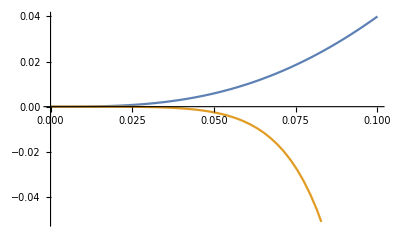

```mathematica
Plot[{exact[Q,0.4],tenorder2[Q,0.4]}, {Q,0,0.1}]
```

```mathematica
Plot[tenorder[Q,0.4],{Q,0,0.2}]
```

-Graphics-